{{0.350298,0.632625},{0.305812,0.547863},{0.403574,0.587539},{0.429079,0.687003},{0.388713,0.5},{0.305812,0.452137},{0.46055,0.546107},{0.48699,0.611636},{0.524107,0.698542},{0.436782,0.408413},{0.485,0.475389},{0.526205,0.537964},{0.576089,0.597015},{0.613613,0.664597},{0.370401,0.431981},{0.350298,0.367375},{0.429079,0.312997},{0.482358,0.354703},{0.539463,0.395945},{0.568218,0.466265},{0.614229,0.526472},{0.677091,0.592945},{0.524107,0.301458},{0.613613,0.335403},{0.608053,0.404273},{0.640163,0.465453},{0.7,0.5},{0.677091,0.407055}}

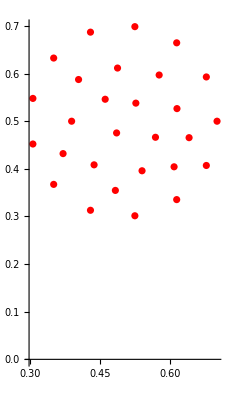

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/2d/square/disk_line/solution/mesh_0/sub_meshes/sub_mesh_0/vertices.csv"];
tabve=Table[{tabve[[i,1]],tabve[[i,2]]},{i,2,Length[tabve]}]
meshplot=ListPlot[tabve,PlotStyle->Red,AspectRatio->Automatic]
```

```mathematica
v = Import ["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/solution/normal_test.csv"];
```

```mathematica
v=Table[{{v[[i,3]],v[[i,4]]},{v[[i,1]],v[[i,2]]}},{i,2,Length[v]}]
```

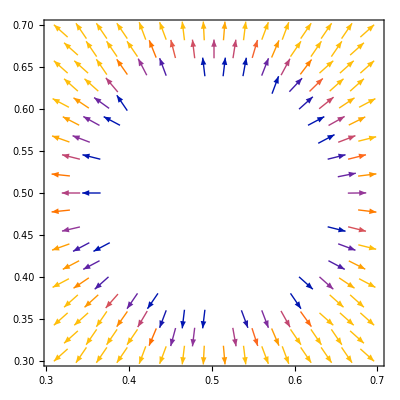

```mathematica
normalplot=ListVectorPlot[v]
```

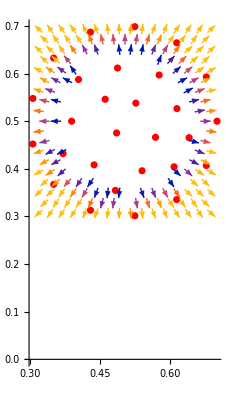

```mathematica
Show[meshplot,normalplot]
```